## SI #: Significance of clustering

Adaptive alleles can resist gene flow more effectively if they are linked.  Thus, if the selected loci responsible for divergence are seen to be clustered on the genetic map, or involved with chromosomal rearrangements that suppress recombination, this suggests that divergence occurred despite gene flow (Rieseberg, 2001).  However, while there are good examples where chromosome rearrangements are associated with selected divergence, evidence for clustering is unclear (Yeaman et al., 2016).  In the hybrid zone between Antirrhinum majus striatum and pseudomajus, ROS and EL are closely linked.  Is this significant evidence for clustering?  Specifically, what is the probability that the closest pair of k loci are closer than ϵ apart?

Assume that k loci, falling uniformly on a map of length R.  Then, the gaps between them are distributed exponentially with rate k/R, .  What is the probability that the (k-1) gaps are all greater than ϵ ?  The chance that one gap is larger than ϵ is exp[-kϵ/R], and so the chance that (k-1) are all larger is exp[-k(k-1) ϵ/R]. This argument assumes independence, which is not quite correct, but simulations show that it is accurate.

Assuming a genetic map of length 5.88 Morgans, the probability that the closest pair are closer than 0.5cM is 1.7% with 5 loci in total, and 7.4% with 10 loci.  Counting ROS/EL/VEN/SULF/FLA gives 5 loci.  Thus, finding this close a linkage is unlikely, and indeed, formally significant.  However, clustering of functional loci on the genetic map (e.g. due to tandem duplication of Myb transcription factors), and variation in recombination rate, would increase this probability. Thus, we regard this linkage as suggestive, but not definitive.

Table Sx1. The probability that the closest pair amongst k genes, thrown down on a linear map of length 5.88 Morgans, are closer than 0.5cM

k | P
5 | 0.0169
6 | 0.0252
7 | 0.0351
8 | 0.0465
9 | 0.0594
10 | 0.0737

It is actually hard to see how clustering could evolve as a result of gene flow in Antirrhinum, which has an extensive geographic  range.  Suppose that one allele becomes established over some broad area, and gives a new floral phenotype that is maintained by positive frequency-dependence.  Further alleles may improve its attractiveness to pollinators, and will be favoured wherever the first allele is sufficiently frequent.  Linkage will aid the establishment of such an allele only within clines where populations are mixed; yet, such clines are  narrow relative to the species’ range, and indeed, we have only found a few of them.  Thus, it is hard to see that they can contribute significantly to clustering.

Alternatively, one could imagine that pairs of alleles are required to establish a new phenotype within a spatially structured population. The probability that these will established can be greatly enhanced by linkage, simply because such events are extremely rare when neighbourhood size is large  (Rouhani and Barton, 1987).   However, this also makes such a mode of establishment highly improbable: it is more likely that alleles are established one at a time, in which case gene flow has little effect.

### References

Rieseberg, L. H. 2001 Chromosomal rearrangements and speciation. Trends in Ecology & Evolution 16: 351-358.

Rouhani S., Barton N. H. 1987 Speciation and the “shifting balance” in a continuous population. Theor. Popul. Biol. 31: 465–492.

Yeaman S., Aeschbacher S., Burger R., 2016 The evolution of genomic islands by increased establishment probability of linked alleles. Mol. Ecol. 25: 1–41.

#### Check by simulation

The linkage map has total length 5.88M

```mathematica
Total[Last/@{{21,1.00},{17,0.85},{16,0.75},{14,0.68},{18,0.78},{21,0.67},{13,0.65},{11,0.50}}]
```

5.88

```mathematica
Table[{k,1-Exp[-k(k-1)ϵ/R]}/.{R->5.88,ϵ->0.005},{k,5,10}]//TableForm
```

5 | 0.016863
6 | 0.0251876
7 | 0.0350841
8 | 0.046503
9 | 0.0593879
10 | 0.0736754

```mathematica
minInt[z_]:=Module[{sz=Sort[z]},Min[Drop[sz,1]-Drop[sz,-1]]];
```

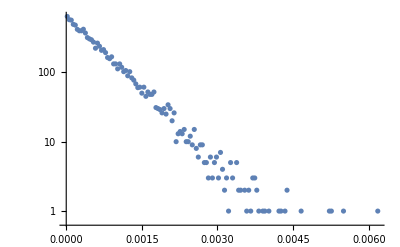

{6.45934-1585.63 x,37}

```mathematica
del=0.00004;
bc10=BinCounts[minInt/@RandomReal[{0,1},{10^4,40}],{0,0.1,del}];tt=Transpose[{Range[del/2,0.1-del/2,del],bc10}];
ListLogPlot[tt]
st=Select[tt,#⟦1⟧<0.0015&];
{Fit[st/.{x_,y_}:>{x,Log[y]},{1,x},x],Length[st]}
```

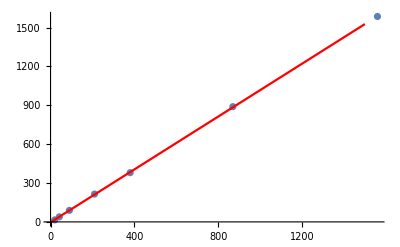

-3.12294+1.01993 x

```mathematica
ff={{5, 15.53}, {7, 39.08}, {10, 88.845}, {15, 214.85}, {20, 379.88}, {30, 889.54}, {40, 1585.63}}/.{x_,y_}:>{x(x-1),y};
ft=Fit[ff,{1,x},x];
Show[ListPlot[ff],Plot[ft,{x,0,1500},{PlotStyle->Red}]]
ft
```